```mathematica
r[x_]:= x+ r0
r0 = 1/(4c);
Veff[x_] := 1/(8r[x]^2) -c/r[x] + 2c^2
```

```mathematica
phiminusone[x_]:= Assuming[x>=0&&c>=0,Simplify[-Sqrt[Simplify[2Veff[x]]]]]
pot[x_] := -c k^2Exp[-b*9*r[x]/k^2]/r[x]
Eminustwo = -2c^2;
```

```mathematica
Eminusone = D[x(-phiminusone[x])some[x]-x(1/2  D[phiminusone[x],x]+1/(2r[x]^2))-phiminusone[x],x] /.x->0;
phizero =Simplify[(x (Eminusone +1/2  D[phiminusone[x],x]+1/(2r[x]^2))+ phiminusone[x])/ (x(-phiminusone[x]))];
COne = phizero /(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2)) /. x->0;
Ezero = D[-x(1/2D[phizero,x]+1/2 phizero^2-3/(8r[x]^2)-SeriesCoefficient[pot[x],{k,Infinity,0}] )+COne(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2))-phizero ,x] /. x->0;
phione = Simplify[(x(Ezero +1/2D[phizero,x]+1/2 phizero^2-3/(8r[x]^2)-SeriesCoefficient[pot[x],{k,Infinity,0}]) -COne(Eminusone+1/2D[phiminusone[x],x]+ phiminusone[x]phizero+1/(2r[x]^2))+phizero) / (x(-phiminusone[x]))];
Ctwo =( -COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-9c*b-3/(8r[x]^2))+phione)/(Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)) /.x->0;
Eone = D[-x(1/2 D[phione,x]+ phione*phizero) +COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-9c*b-3/(8r[x]^2))+Ctwo((Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)))-phione,x] /. x->0;
phitwo = Simplify[(x(Eone+1/2 D[phione,x]+ phione*phizero) -COne(Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero[x]^2-9c*b-3/(8r[x]^2))-Ctwo((Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)))+phione)/ (x(-phiminusone[x]))];
```

```mathematica
phi[n_] := phi[n] = Which[n==-1,phiminusone[x],n==0, phizero, n==1, phione, n==2, phitwo,True,Simplify[ (x(1/2 D[phi[n-1],x]+Energy[n-1]+ 1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}]+ termone[n])-
Sum[Cs[m](Energy[n-m-1]+1/2D[phi[n-1-m],x]+1/2Sum[phi[p]phi[n-m-p-1] ,{p,-1,n-m}]+termtwo[n,m]),{m,1,n-2}]-Cs[n-1](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-9c*b-3/(8r[x]^2))-Cs[n] (Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2))+phi[n-1])/(-x*phiminusone[x])]]
Cs[n_]:= Cs[n] = Which [n==1,COne,n== 2,Ctwo,True,Simplify[(-Sum[Cs[m](Energy[n-m-1]+1/2D[phi[n-m-1],x]+1/2Sum[phi[p]phi[n-m-p-1] ,{p,-1,n-m}]+termtwo[n,m]),{m,1,n-2}]-Cs[n-1](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-9c*b-3/(8r[x]^2))+phi[n-1])/(Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2)) /. x->0]]
Energy[n_]:= Energy[n]= Which[n==-2,Eminustwo,n==-1,Eminusone,n==0,Ezero,n==1,Eone,True,Simplify[D[-x(1/2 D[phi[n],x]+ 1/2Sum[phi[m]phi[n-m],{m,0,n}]+ termone[n+1])+
Sum[Cs[m](Energy[n-m]+1/2D[phi[n-m],x]+1/2Sum[phi[p]phi[n-m-p] ,{p,-1,n-m+1}]+termtwo[n+1,m]),{m,1,n-1}]+Cs[n](Ezero+1/2D[phizero,x]+phione*phiminusone[x]+1/2 phizero^2-9c*b-3/(8r[x]^2))+Cs[n+1] (Eminusone+1/2D[phiminusone[x],x]+phizero*phiminusone[x]+1/(2r[x]^2))-phi[n],x] /. x->0]]
termtwo[n_,m_] := Which[EvenQ[m]&& EvenQ[n] ||OddQ[m]&& OddQ[n],0,True,(-1)^((n-m+1)/2) (9b)^((n-m+1)/2 )/Factorial[((n-m+1)/2) ] *c*r[x]^(((n-m-1)/2) )]
termone[n_]:= Which[EvenQ[n],0,True, (-1)^((n+1)/2)(9b)^((n+1)/2)/Factorial[(n+1)/2]c r[x]^((n-1)/2)]
```

```mathematica
Clear[Energy,phi,Cs]
```

```mathematica
Clear[c]
c = 1/9
```

1/9

```mathematica
Energy[147]
```

$Aborted

```mathematica
perturbationorder=26
```

26

```mathematica
perturbationorder=37
maxkOrder = 145
```

37

145

```mathematica
EnergySeries = Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder}]+O[b]^(perturbationorder+1),b];
EnergySeriesplusOne= Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder+1}],k],b]],b]+O[b]^(perturbationorder+1)];
Coefficients = {-2/(k+1)^2};
Do[AppendTo[Coefficients,Collect[Coefficient[EnergySeries, b,n],k] ],{n,1,perturbationorder}]
Coefficientstwo = {-2/(k+1)^2};
Do[AppendTo[Coefficientstwo,Collect[Coefficient[EnergySeriesplusOne, b,n],k] ],{n,1,perturbationorder}]
Table[Coefficients[[n]] -Coefficientstwo[[n]],{n,1,perturbationorder+1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Simplify[Sum[1/k^2 (-1)^(n+1)(4+2(n-1))/k^n,{n,1,Infinity}] -2/k^2 /. k->l]
```

-2/(1+l)^2

```mathematica
(*Table[Length[Coefficients[[n]] /. Sum ->List],{n,1,perturbationorder+1}]*)
```

```mathematica
k=3
```

3

```mathematica
PartialSum = Table[Total[Take[Coefficients,order+1]*Table[b^n,{n,0,order}]],{order,0,perturbationorder}];
```

```mathematica
value = 0.20
N[PadeApproximant[Simplify[PartialSum[[perturbationorder+1]] /a^2] ,{b,0,Floor[perturbationorder/2]}] /. b->value]
```

0.2

-0.0121079/a^2

```mathematica
NumberForm[-0.012107865770455367,16]
```

-0.01210786577045537

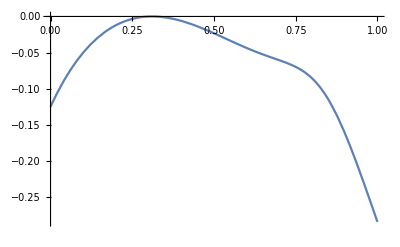

```mathematica
Plot[N[PadeApproximant[Simplify[PartialSum[[perturbationorder+1]] ] ,{b,0,Floor[perturbationorder/2]}] /. b->s],{s,0,1}]
```

```mathematica
N[PartialSum[[perturbationorder+1]]/a^2 /. g->0.3]
```

-1.75384×10^11

```mathematica
NMaximize[function[s],s]
```

{-1.77418×10^-10,{s→0.310209}}

```mathematica
function[s_] := Which[s>= 0 && s<=0.5, N[PadeApproximant[Simplify[PartialSum[[perturbationorder+1]] ] ,{b,0,Floor[perturbationorder/2]}] /. b->s],True,-1]
```

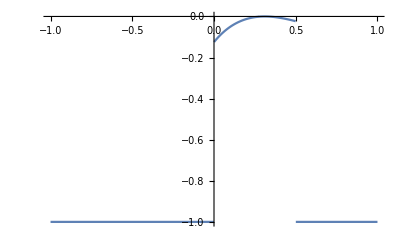

```mathematica
Plot[function[s],{s,-1,1}]
```

```mathematica
k=3
```

3

```mathematica
N[function[0.31]]
```

-3.81678×10^-8

```mathematica
NumberForm[-0.1152932851679943,16]
```

-0.1152932851679943

```mathematica
Clear[k]
```

```mathematica
Clear[k]
```